```mathematica
<<xlr8r.m
```

interpret::shdw: Symbol "interpret" appears in multiple contexts {"xlr8r`", "Global`"}; definitions in context "xlr8r`" may shadow or be shadowed by other definitions.

xCellerator 0.95 (28-Feb-2014) loaded Tue 23 Aug 2016 18:56:51
using Mathematica 8.0 for Microsoft Windows (64-bit) (October 6, 2011) (Version 8., Release 4)

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.15 (4-April-2013)) loaded Tue 23 Aug 2016 18:56:58
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

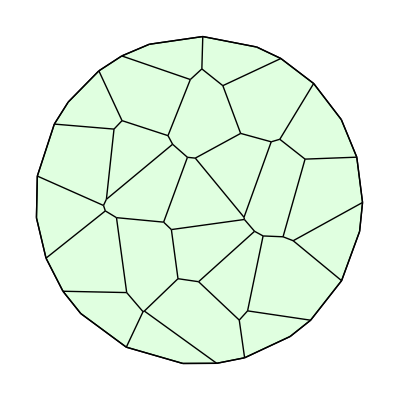

```mathematica
ww = TemplateRandomCircularGrid[20,10];
ShowTissue[ww]
```

```mathematica
net = {
{A->B,b},
{2 A+B->3 A,c},
{cell -> cell + cell,a};
}
```

{{A→B,b},{2 A+B→3 A,c},Null}

```mathematica
interpret[net][[1]]//TableForm
```

Not a list of lists.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧